```mathematica
r[x_]:= x+ r0

r0 = 1/(4 c);
Veff[x_] := 1/(8r[x]^2) -c/r[x] + 2c^2
```

```mathematica
phiminusone[x_]:= Assuming[x>=0&&c>=0,Simplify[-Sqrt[Simplify[2Veff[x]]]]]
pot[x_] := -c k^2Exp[-b*9*r[x]/k^2]/r[x]
Eminustwo = -2c^2;
Es = {Eminustwo};
phis = {phiminusone[x]};
Eminusone = -1/2(D[phis[[1]],x] /. x-> 0)-1/(2 r[0]^2);
AppendTo[Es,Eminusone];
phizero[s_] :=Simplify[( Es[[2]] + 1/(2r[s]^2) +1/2(D[phis[[1]],x] /.x->s))/(-phiminusone[s])]
AppendTo[phis,phizero[x]];

Ezero = 3/(8 r[0]^2)-1/2(D[phis[[2]],x]/. x->0)-1/2( phis[[2]]^2 /. x->0) +SeriesCoefficient[pot[x],{k,Infinity,0}] /. x->0;
phione[s_] := Simplify[(-3/(8 r[s]^2)+1/2(D[phis[[2]],x]/. x->s)+1/2( phis[[2]]^2 /. x->s) -SeriesCoefficient[pot[x],{k,Infinity,0}] + Ezero)/(-phiminusone[s])]
```

```mathematica
Energy[n_]:= Energy[n] = Which[n==-2,Eminustwo,n==-1,Eminusone,n==0,Ezero,True, Simplify[-1/2(D[phi[n],x]/.x->0)-1/2Sum[(phi[m]/.x->0)(phi[n-m]/. x->0),{m,0,n}]+(SeriesCoefficient[pot[x],{k,Infinity,n}]/. x->0)]]
phi[n_]:= phi[n] = Which[n==-1,phiminusone[x],n==0,phizero[x],n==1,phione[x],True,Simplify[(Energy[n-1]+ 1/2 D[phi[n-1],x]+1/2Sum[phi[m]phi[n-m-1],{m,0,n-1}]- SeriesCoefficient[pot[x],{k,Infinity,n-1}])/(-phiminusone[x])]]
```

```mathematica
Clear[phi,Energy]
```

```mathematica
Clear[c]
```

```mathematica
c=1/9
```

1/9

```mathematica
maxkOrder = 99
perturbationorder = 20
EnergySeries = Expand[Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder}],k],b]],b]] + O[b]^(perturbationorder+1)] ;
EnergySeriesplusOne= Normal[Collect[Simplify[Collect[Collect[Sum[k^(-n)Energy[n],{n,-2,maxkOrder+1}],k],b]],b]+O[b]^(perturbationorder+1)];
```

99

20

```mathematica
Coefficients = {-2/(k-1)^2};
Do[AppendTo[Coefficients,Collect[Coefficient[EnergySeries, b,n],k] ],{n,1,perturbationorder}]
Coefficientstwo = {-2/(k-1)^2};
Do[AppendTo[Coefficientstwo,Collect[Coefficient[EnergySeriesplusOne, b,n],k] ],{n,1,perturbationorder}]
```

```mathematica
(*Table[Length[Coefficients[[n]] /. Sum ->List],{n,1,perturbationorder+1}]*)
Table[Coefficients[[n]] -Coefficientstwo[[n]],{n,1,perturbationorder+1}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
k =3
```

3

```mathematica
PartialSums = Table[Total[Take[Coefficients,order+1]*Table[b^n,{n,0,order}]],{order,0,perturbationorder}];
PadeNN = Table[PadeApproximant[PartialSums[[n]],{b,0,Floor[n/2]}] ,{n,3,perturbationorder}];
PadeNNplusone = Table[PadeApproximant[PartialSums[[n]],{b,0,{Floor[n/2],Floor[n/2]+1}}] ,{n,3,perturbationorder}];
```

```mathematica
value = 1
N[PartialSums[[perturbationorder+1]]/. b->value];
BestEstimatePade= N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->value]
```

1

-0.0102858

```mathematica
Clear[k]
```

```mathematica
TotalSeries = Collect[Sum[k^(-n)Energy[n],{n,-2,200}],k] /.k->l;
l = 1/y
```

1/y

```mathematica
k=3
```

3

```mathematica
N[PadeApproximant[TotalSeries  /. b->0.5,{y,0,Floor[200/2]}] /. y->1/3]
```

N::precsm: Requested precision -66.446 is smaller than $MinPrecision. Using $MinPrecision instead.

-0.148118

```mathematica
-0.02431419382750902
```

```mathematica
NumberForm[-0.30633448845212025,16]
```

-0.3063344884521202

```mathematica
value = 1.19;
```

```mathematica
TotalSeries = Collect[Sum[k^(-n)Energy[n],{n,-2,200}],k] /.k->l;
N[PadeApproximant[TotalSeries  /. b->value,{y,0,Floor[200/2]}] /. y->1/3]
```

N::precsm: Requested precision -57.4454 is smaller than $MinPrecision. Using $MinPrecision instead.

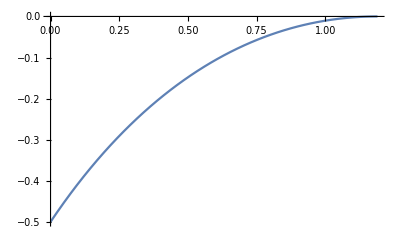

```mathematica
Plot[N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->s],{s,0,1.19}]
```

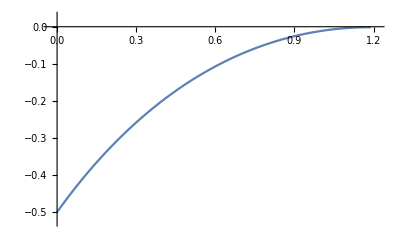

```mathematica
Abs[ NMaximize[function[s],{s}][[2]][[1]]]
```

Abs[s→-1.19061]

```mathematica
N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->10]
```

-12.4156

```mathematica
list = Table[{s,N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->s]},{s,0,1.19,0.01}];
```

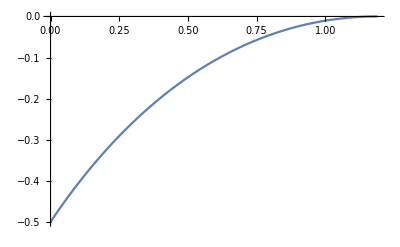

```mathematica
ListPlot[list,DataRange->{0,1.19},Joined->True]
```

```mathematica
Export["test.txt",list,"Table","FieldSeparators"->" "]
```

test.txt

```mathematica
Clear[k]
```

```mathematica
Energy[201];
```

```mathematica
function[s_] := Which[s>= 0, N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->s],True, N[PadeApproximant[PartialSums[[perturbationorder]],{b,0,Floor[perturbationorder/2]}]/. b->-s]]
```

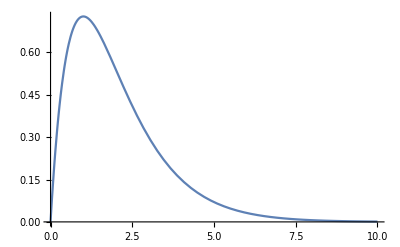

```mathematica
value =0.1;
phiss = Integrate[Sum[phi[n]k^(-n)/. b->value ,{n,-1,100}] ,x];
u = Exp[phiss] /. x-> (d-r0);
psi = d^(-2)u ;
Plot[Cs*u,{d,0,10}]
```

```mathematica
c=1/9
k=3
```

1/9

3

```mathematica
L = NIntegrate[u^2,{d,0,10}]
Cs = Sqrt[1/L]
```

0.253409

1.9865

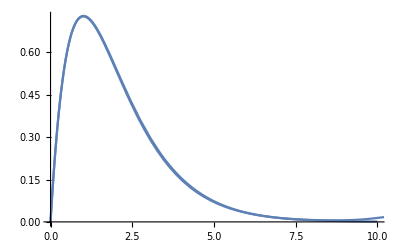

```mathematica
phiss=Integrate[Sum[phi[n]k^(-n)/. b->0.15,{n,-1,100}],x];
su=Exp[phiss]/. x->(d-r0);
psi=d^(-2)u;
Show[Plot[Cs*u,{d,0,10}],Plot[Csu*su,{d,0,15}]]
```

```mathematica
L = NIntegrate[su^2,{d,0,10}]
Csu = Sqrt[1/L]
```

0.257312

1.97138

```mathematica
PartialSums[[Length[PartialSums]]] /. b->0.4
```

-2.36795

```mathematica
PadeNN[[Length[PadeNN]]] /. b->0.
```

-0.257639

```mathematica
Exp[PadeApproximant[phiss,{x,0,25}]]
```

1.23254×10^-54

```mathematica
maxDegree=ResourceFunction["PolynomialDegree"][Collect[Integrate[Sum[phi[n]k^(-n)/. b->0.15,{n,-1,100}],x],x]-0.9999999999999999 Log[2.25+1. x],x]
```

50

```mathematica
initial = Collect[Integrate[Sum[phi[n]k^(-n)/. b->0.2,{n,-1,100}],x],x];
```

```mathematica
phiss = PadeApproximant[initial,{x,0,Floor[maxDegree/2]}];
```

```mathematica
su=Exp[phiss]/. x->(d-r0);
```

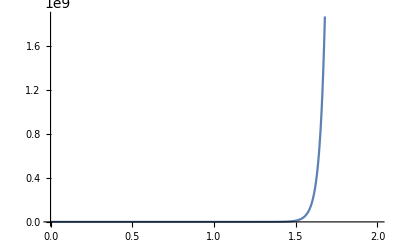

```mathematica
Plot[su,{d,0,2}]
```

```mathematica
phiss /. x->0.1
```

1.72328×10^9

```mathematica
Clear[k]
```

```mathematica
a= Integrate[Sum[phi[n]k^(-n),{n,-1,20}],x]
```

1/211392921600(-(46976204800 x)/k^2-(46976204800 x)/k-11744051200 (9+4 x)-11744051200 k (9+4 x)+(1468006400 x (-32+729 b^2 (9+2 x)))/k^3-(1468006400 x (32+729 b^2 (9+2 x)))/k^4+(734003200 x (-64+729 b^3 (243+81 x+8 x^2)))/k^6-(734003200 x (64+729 b^3 (243+81 x+8 x^2)))/k^5+(22937600 x (-2048+314928 b^3 (9+2 x)+19683 b^4 (6561+2430 x+336 x^2+16 x^3)))/k^7-(22937600 x (2048+314928 b^3 (9+2 x)+19683 b^4 (13851+4860 x+576 x^2+16 x^3)))/k^8-(458752 x (102400-35429400 b^4 (162+63 x+8 x^2)+177147 b^5 (885735+364500 x+64800 x^2+5400 x^3+128 x^4)))/k^9+(458752 x (-102400-2952450 b^4 (-1701-324 x+16 x^2)+177147 b^5 (2066715+856575 x+152280 x^2+11880 x^3+128 x^4)))/k^10-1/k^12 114688 x (409600-318864600 b^4 (9+2 x)-15943230 b^5 (-169857-51030 x-3600 x^2+112 x^3)+177147 b^6 (318864600+140241375 x+28737180 x^2+3100680 x^3+134784 x^4+640 x^5))+1/k^11 28672 x (-1638400-7652750400 b^4 (9+2 x)-510183360 b^5 (-729+729 x+414 x^2+50 x^3)+177147 b^6 (429581475+187972650 x+38491200 x^2+4276800 x^3+214272 x^4+2560 x^5))+1/(7 k^14)2048 x (-160563200-899963447040 b^5 (-243-27 x+8 x^2)-11249543088 b^6 (-3455460-1077705 x-90090 x^2+1200 x^3+224 x^4)+23914845 b^7 (30300108615+14594314644 x+3580101504 x^2+516382776 x^3+37812096 x^4+919296 x^5+2048 x^6))-1/(7 k^13)1024 x (321126400-224990861760 b^5 (6804+2295 x+232 x^2)-3749847696 b^6 (3674160+2525985 x+780840 x^2+103680 x^3+4352 x^4)+4782969 b^7 (97373277225+45426395700 x+10630569600 x^2+1480278240 x^3+110750976 x^4+3386880 x^5+20480 x^6))+1/(7 k^15)160 x (-2055208960-563737103225856 b^5 (9+2 x)-12959473637376 b^6 (38151+13446 x+1658 x^2+62 x^3)-19284931008 b^7 (-55624158+46524051 x+36665784 x^2+8412336 x^3+749952 x^4+13568 x^5)+43046721 b^8 (2345295368367+1146672176706 x+295589846160 x^2+48377664720 x^3+4764324096 x^4+245887488 x^5+4681728 x^6+14336 x^7))-1/(7 k^16)32 x (10276044800-777568418242560 b^5 (9+2 x)-1349945170560 b^6 (-531441-80028 x+14544 x^2+1088 x^3)-96424655040 b^7 (-1735568208-632447595 x-83106000 x^2-2277720 x^3+385920 x^4+4352 x^5)+43046721 b^8 (39686278725135+20129911569180 x+5484962407680 x^2+944869030560 x^3+95315222016 x^4+4705827840 x^5+66355200 x^6+71680 x^7))-1/(7 k^17)32 x (10276044800-404983551168000 b^6 (4374+1161 x+56 x^2)+3471287581440 b^7 (-46222245-20266200 x-3867750 x^2-298440 x^3+1312 x^4)-3099363912 b^8 (-79163451360+52905837285 x+49324373280 x^2+13832804160 x^3+1804311936 x^4+97211520 x^5+885760 x^6)+4782969 b^9 (3668676383483055+1873744989630570 x+526113006368040 x^2+98296007604480 x^3+11853962983296 x^4+851346961920 x^5+30658590720 x^6+370137600 x^7+573440 x^8))+1/(7 k^18)16 x (-20552089600-8099671023360 b^6 (87723+26568 x+2096 x^2)-520693137216 b^7 (-519051645-100040670 x+13564800 x^2+3023760 x^3+4864 x^4)-3874204890 b^8 (-3673961641287-1455413770440 x-240141627936 x^2-15748102944 x^3+719663616 x^4+111025152 x^5+462848 x^6)+4782969 b^9 (25033773461390505+13485256188415830 x+4098677277920400 x^2+827101227844080 x^3+105447463172352 x^4+7665355918080 x^5+253965404160 x^6+2151152640 x^7+1146880 x^8))-1/(35 k^20)2 x (822083584000-1145941456384972800 b^6 (9+2 x)+624831764659200 b^7 (-18294984-6803271 x-801504 x^2+3224 x^3)+9762996322800 b^8 (87446195541+24926157540 x+833276160 x^2-369113760 x^3-36882432 x^4+73216 x^5)-15496819560 b^9 (-1879326738368415-813649151446425 x-163051958822760 x^2-16148397981240 x^3-63266095872 x^4+107565615360 x^5+4227655680 x^6+8565760 x^7)+387420489 b^10 (450028203719211495+253549073378439090 x+83673482763674160 x^2+19061687396702160 x^3+2904047128442880 x^4+277801767936000 x^5+14742288230400 x^6+330058229760 x^7+1727201280 x^8+458752 x^9))+1/(35 k^19)x (-1644167168000-6123351293660160000 b^6 (9+2 x)+624831764659200 b^7 (-80517321-24219324 x-1687536 x^2+62336 x^3)+234311911747200 b^8 (-4025271915-2023751385 x-499835448 x^2-63157968 x^3-2738304 x^4+49408 x^5)-123974556480 b^9 (-47485961932815-6702294743550 x+5646810992760 x^2+2527296215850 x^3+463800974112 x^4+40104529920 x^5+1290447360 x^6+6496000 x^7)+387420489 b^10 (261746867034748935+138566342406671550 x+41702806196755200 x^2+8662698155422080 x^3+1222639230113280 x^4+111558079180800 x^5+5949423820800 x^6+150876794880 x^7+1172111360 x^8+917504 x^9))+105696460800 (-1+k) Log[9+4 x])

```mathematica
phisss = PadeApproximant[a,{k,Infinity,7}];
```

```mathematica
u = Exp[phisss]/. {x->(d-r0),k->3,b->0.1}
```

ⅇ^((1/18 (-9-4 (-9/4+d)+9 Log[9+4 (-9/4+d)])+(-5.96166×10^24-1.18993×10^25 (-9/4+d)-1.05553×10^25 (-9/4+d)^2-5.51933×10^24 (-9/4+d)^3-1.89979×10^24 (-9/4+d)^4-4.55322×10^23 (-9/4+d)^5-7.84193×10^22 (-9/4+d)^6-9.86302×10^21 (-9/4+d)^7-9.07236×10^20 (-9/4+d)^8-6.00493×10^19 (-9/4+d)^9-2.75524×10^18 (-9/4+d)^10-8.23673×10^16 (-9/4+d)^11-1.4791×10^15 (-9/4+d)^12-1.80072×10^13 (-9/4+d)^13-1.70949×10^11 (-9/4+d)^14+1.64207×10^9 (-9/4+d)^15+1.12447×10^7 (-9/4+d)^16+5.89466×10^24 Log[9+4 (-9/4+d)]+8.51423×10^24 (-9/4+d) Log[9+4 (-9/4+d)]+5.56534×10^24 (-9/4+d)^2 Log[9+4 (-9/4+d)]+2.1877×10^24 (-9/4+d)^3 Log[9+4 (-9/4+d)]+5.78783×10^23 (-9/4+d)^4 Log[9+4 (-9/4+d)]+1.08897×10^23 (-9/4+d)^5 Log[9+4 (-9/4+d)]+1.49293×10^22 (-9/4+d)^6 Log[9+4 (-9/4+d)]+1.49346×10^21 (-9/4+d)^7 Log[9+4 (-9/4+d)]+1.06886×10^20 (-9/4+d)^8 Log[9+4 (-9/4+d)]+5.23835×10^18 (-9/4+d)^9 Log[9+4 (-9/4+d)]+1.61527×10^17 (-9/4+d)^10 Log[9+4 (-9/4+d)]+2.58432×10^15 (-9/4+d)^11 Log[9+4 (-9/4+d)]+1.26143×10^13 (-9/4+d)^12 Log[9+4 (-9/4+d)]+1.14033×10^11 (-9/4+d)^13 Log[9+4 (-9/4+d)]+6.77168×10^9 (-9/4+d)^14 Log[9+4 (-9/4+d)]-5.53679×10^7 (-9/4+d)^15 Log[9+4 (-9/4+d)])/(54 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(5.00654×10^26+7.88603×10^26 (-9/4+d)+5.23643×10^26 (-9/4+d)^2+1.8621×10^26 (-9/4+d)^3+3.50071×10^25 (-9/4+d)^4+1.47499×10^24 (-9/4+d)^5-9.87884×10^23 (-9/4+d)^6-2.99506×10^23 (-9/4+d)^7-4.74597×10^22 (-9/4+d)^8-4.97511×10^21 (-9/4+d)^9-3.62544×10^20 (-9/4+d)^10-1.81934×10^19 (-9/4+d)^11-5.93591×10^17 (-9/4+d)^12-1.13647×10^16 (-9/4+d)^13-1.27104×10^14 (-9/4+d)^14-1.37164×10^12 (-9/4+d)^15+1.17486×10^10 (-9/4+d)^16+9.89044×10^7 (-9/4+d)^17+4.59884×10^26 Log[9+4 (-9/4+d)]+6.57224×10^26 (-9/4+d) Log[9+4 (-9/4+d)]+4.29306×10^26 (-9/4+d)^2 Log[9+4 (-9/4+d)]+1.71936×10^26 (-9/4+d)^3 Log[9+4 (-9/4+d)]+4.76886×10^25 (-9/4+d)^4 Log[9+4 (-9/4+d)]+9.74892×10^24 (-9/4+d)^5 Log[9+4 (-9/4+d)]+1.51313×10^24 (-9/4+d)^6 Log[9+4 (-9/4+d)]+1.79712×10^23 (-9/4+d)^7 Log[9+4 (-9/4+d)]+1.61701×10^22 (-9/4+d)^8 Log[9+4 (-9/4+d)]+1.06942×10^21 (-9/4+d)^9 Log[9+4 (-9/4+d)]+4.89414×10^19 (-9/4+d)^10 Log[9+4 (-9/4+d)]+1.37053×10^18 (-9/4+d)^11 Log[9+4 (-9/4+d)]+1.64015×10^16 (-9/4+d)^12 Log[9+4 (-9/4+d)]-5.94158×10^13 (-9/4+d)^13 Log[9+4 (-9/4+d)]+5.64021×10^11 (-9/4+d)^14 Log[9+4 (-9/4+d)]+5.83219×10^10 (-9/4+d)^15 Log[9+4 (-9/4+d)]-4.34546×10^8 (-9/4+d)^16 Log[9+4 (-9/4+d)])/(15552 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(2.90568×10^26+4.98493×10^26 (-9/4+d)+3.64594×10^26 (-9/4+d)^2+1.51162×10^26 (-9/4+d)^3+3.98986×10^25 (-9/4+d)^4+7.18192×10^24 (-9/4+d)^5+9.35471×10^23 (-9/4+d)^6+9.46502×10^22 (-9/4+d)^7+8.06515×10^21 (-9/4+d)^8+5.95917×10^20 (-9/4+d)^9+3.41806×10^19 (-9/4+d)^10+1.10519×10^18 (-9/4+d)^11-7.89882×10^15 (-9/4+d)^12-2.35723×10^15 (-9/4+d)^13-7.93169×10^13 (-9/4+d)^14-5.0416×10^11 (-9/4+d)^15+1.87974×10^10 (-9/4+d)^16-4.71136×10^7 (-9/4+d)^17-6.6997×10^26 Log[9+4 (-9/4+d)]-9.38274×10^26 (-9/4+d) Log[9+4 (-9/4+d)]-5.89764×10^26 (-9/4+d)^2 Log[9+4 (-9/4+d)]-2.21071×10^26 (-9/4+d)^3 Log[9+4 (-9/4+d)]-5.53974×10^25 (-9/4+d)^4 Log[9+4 (-9/4+d)]-9.84952×10^24 (-9/4+d)^5 Log[9+4 (-9/4+d)]-1.28269×10^24 (-9/4+d)^6 Log[9+4 (-9/4+d)]-1.23681×10^23 (-9/4+d)^7 Log[9+4 (-9/4+d)]-8.73074×10^21 (-9/4+d)^8 Log[9+4 (-9/4+d)]-4.32882×10^20 (-9/4+d)^9 Log[9+4 (-9/4+d)]-1.36107×10^19 (-9/4+d)^10 Log[9+4 (-9/4+d)]-1.89136×10^17 (-9/4+d)^11 Log[9+4 (-9/4+d)]+2.81516×10^15 (-9/4+d)^12 Log[9+4 (-9/4+d)]+1.54638×10^14 (-9/4+d)^13 Log[9+4 (-9/4+d)]+1.29741×10^12 (-9/4+d)^14 Log[9+4 (-9/4+d)]-4.04323×10^10 (-9/4+d)^15 Log[9+4 (-9/4+d)]+1.06006×10^8 (-9/4+d)^16 Log[9+4 (-9/4+d)])/(5184 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(2.97971×10^28+6.59297×10^28 (-9/4+d)+6.19281×10^28 (-9/4+d)^2+3.36711×10^28 (-9/4+d)^3+1.20436×10^28 (-9/4+d)^4+3.03544×10^27 (-9/4+d)^5+5.61245×10^26 (-9/4+d)^6+7.77831×10^25 (-9/4+d)^7+8.11635×10^24 (-9/4+d)^8+6.28319×10^23 (-9/4+d)^9+3.46399×10^22 (-9/4+d)^10+1.24255×10^21 (-9/4+d)^11+2.23002×10^19 (-9/4+d)^12-1.13586×10^17 (-9/4+d)^13-1.26169×10^16 (-9/4+d)^14-1.8643×10^14 (-9/4+d)^15-7.28673×10^11 (-9/4+d)^16-1.57902×10^8 (-9/4+d)^17+2.23085×10^8 (-9/4+d)^18+4.16636×10^27 Log[9+4 (-9/4+d)]+6.64609×10^27 (-9/4+d) Log[9+4 (-9/4+d)]+4.78394×10^27 (-9/4+d)^2 Log[9+4 (-9/4+d)]+2.05427×10^27 (-9/4+d)^3 Log[9+4 (-9/4+d)]+5.90264×10^26 (-9/4+d)^4 Log[9+4 (-9/4+d)]+1.21853×10^26 (-9/4+d)^5 Log[9+4 (-9/4+d)]+1.92057×10^25 (-9/4+d)^6 Log[9+4 (-9/4+d)]+2.44807×10^24 (-9/4+d)^7 Log[9+4 (-9/4+d)]+2.61612×10^23 (-9/4+d)^8 Log[9+4 (-9/4+d)]+2.30946×10^22 (-9/4+d)^9 Log[9+4 (-9/4+d)]+1.57226×10^21 (-9/4+d)^10 Log[9+4 (-9/4+d)]+7.39876×10^19 (-9/4+d)^11 Log[9+4 (-9/4+d)]+1.97641×10^18 (-9/4+d)^12 Log[9+4 (-9/4+d)]+1.15018×10^16 (-9/4+d)^13 Log[9+4 (-9/4+d)]-5.97327×10^14 (-9/4+d)^14 Log[9+4 (-9/4+d)]-3.67301×10^12 (-9/4+d)^15 Log[9+4 (-9/4+d)]+1.29536×10^11 (-9/4+d)^16 Log[9+4 (-9/4+d)]-7.01925×10^8 (-9/4+d)^17 Log[9+4 (-9/4+d)])/(3499200 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(1.16609×10^28+2.44879×10^28 (-9/4+d)+2.18032×10^28 (-9/4+d)^2+1.11773×10^28 (-9/4+d)^3+3.73886×10^27 (-9/4+d)^4+8.71634×10^26 (-9/4+d)^5+1.47041×10^26 (-9/4+d)^6+1.83203×10^25 (-9/4+d)^7+1.6999×10^24 (-9/4+d)^8+1.17344×10^23 (-9/4+d)^9+5.97407×10^21 (-9/4+d)^10+2.2089×10^20 (-9/4+d)^11+5.67031×10^18 (-9/4+d)^12+6.38518×10^16 (-9/4+d)^13-2.94683×10^15 (-9/4+d)^14-1.59055×10^14 (-9/4+d)^15-1.54935×10^12 (-9/4+d)^16+2.43417×10^10 (-9/4+d)^17-2.96273×10^7 (-9/4+d)^18-1.09814×10^28 Log[9+4 (-9/4+d)]-1.72503×10^28 (-9/4+d) Log[9+4 (-9/4+d)]-1.24052×10^28 (-9/4+d)^2 Log[9+4 (-9/4+d)]-5.40744×10^27 (-9/4+d)^3 Log[9+4 (-9/4+d)]-1.59585×10^27 (-9/4+d)^4 Log[9+4 (-9/4+d)]-3.37569×10^26 (-9/4+d)^5 Log[9+4 (-9/4+d)]-5.28458×10^25 (-9/4+d)^6 Log[9+4 (-9/4+d)]-6.22261×10^24 (-9/4+d)^7 Log[9+4 (-9/4+d)]-5.52309×10^23 (-9/4+d)^8 Log[9+4 (-9/4+d)]-3.64167×10^22 (-9/4+d)^9 Log[9+4 (-9/4+d)]-1.7144×10^21 (-9/4+d)^10 Log[9+4 (-9/4+d)]-5.26801×10^19 (-9/4+d)^11 Log[9+4 (-9/4+d)]-8.14042×10^17 (-9/4+d)^12 Log[9+4 (-9/4+d)]+2.89218×10^15 (-9/4+d)^13 Log[9+4 (-9/4+d)]+2.94919×10^14 (-9/4+d)^14 Log[9+4 (-9/4+d)]+2.51264×10^12 (-9/4+d)^15 Log[9+4 (-9/4+d)]-4.2081×10^10 (-9/4+d)^16 Log[9+4 (-9/4+d)]+6.66614×10^7 (-9/4+d)^17 Log[9+4 (-9/4+d)])/(777600 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(-2.66826×10^29-5.53284×10^29 (-9/4+d)-5.2851×10^29 (-9/4+d)^2-3.06357×10^29 (-9/4+d)^3-1.20083×10^29 (-9/4+d)^4-3.36797×10^28 (-9/4+d)^5-6.9867×10^27 (-9/4+d)^6-1.09272×10^27 (-9/4+d)^7-1.29886×10^26 (-9/4+d)^8-1.16889×10^25 (-9/4+d)^9-7.81201×10^23 (-9/4+d)^10-3.71375×10^22 (-9/4+d)^11-1.14942×10^21 (-9/4+d)^12-1.87316×10^19 (-9/4+d)^13-5.53362×10^16 (-9/4+d)^14+3.79523×10^14 (-9/4+d)^15-4.70506×10^13 (-9/4+d)^16-1.52296×10^11 (-9/4+d)^17-2.62276×10^9 (-9/4+d)^18+3.47432×10^7 (-9/4+d)^19+4.49089×10^29 Log[9+4 (-9/4+d)]+6.76436×10^29 (-9/4+d) Log[9+4 (-9/4+d)]+4.65055×10^29 (-9/4+d)^2 Log[9+4 (-9/4+d)]+1.93764×10^29 (-9/4+d)^3 Log[9+4 (-9/4+d)]+5.4771×10^28 (-9/4+d)^4 Log[9+4 (-9/4+d)]+1.11302×10^28 (-9/4+d)^5 Log[9+4 (-9/4+d)]+1.67634×10^27 (-9/4+d)^6 Log[9+4 (-9/4+d)]+1.89179×10^26 (-9/4+d)^7 Log[9+4 (-9/4+d)]+1.58731×10^25 (-9/4+d)^8 Log[9+4 (-9/4+d)]+9.60346×10^23 (-9/4+d)^9 Log[9+4 (-9/4+d)]+3.90767×10^22 (-9/4+d)^10 Log[9+4 (-9/4+d)]+8.96937×10^20 (-9/4+d)^11 Log[9+4 (-9/4+d)]+4.29719×10^18 (-9/4+d)^12 Log[9+4 (-9/4+d)]-1.94996×10^17 (-9/4+d)^13 Log[9+4 (-9/4+d)]+1.68965×10^15 (-9/4+d)^14 Log[9+4 (-9/4+d)]+1.18046×10^14 (-9/4+d)^15 Log[9+4 (-9/4+d)]-5.69276×10^11 (-9/4+d)^16 Log[9+4 (-9/4+d)]+1.47199×10^10 (-9/4+d)^17 Log[9+4 (-9/4+d)]-7.81721×10^7 (-9/4+d)^18 Log[9+4 (-9/4+d)])/(74649600 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(-3.57958×10^29-5.47445×10^29 (-9/4+d)-3.92719×10^29 (-9/4+d)^2-1.78089×10^29 (-9/4+d)^3-5.77403×10^28 (-9/4+d)^4-1.41852×10^28 (-9/4+d)^5-2.69771×10^27 (-9/4+d)^6-3.97143×10^26 (-9/4+d)^7-4.46632×10^25 (-9/4+d)^8-3.7337×10^24 (-9/4+d)^9-2.20219×10^23 (-9/4+d)^10-8.24739×10^21 (-9/4+d)^11-1.51649×10^20 (-9/4+d)^12-8.24096×10^17 (-9/4+d)^13-1.19432×10^17 (-9/4+d)^14-7.26011×10^15 (-9/4+d)^15-7.86432×10^13 (-9/4+d)^16+7.15876×10^11 (-9/4+d)^17-5.86212×10^9 (-9/4+d)^18+3.47432×10^7 (-9/4+d)^19-3.57958×10^29 Log[9+4 (-9/4+d)]-5.40258×10^29 (-9/4+d) Log[9+4 (-9/4+d)]-3.72386×10^29 (-9/4+d)^2 Log[9+4 (-9/4+d)]-1.55733×10^29 (-9/4+d)^3 Log[9+4 (-9/4+d)]-4.4269×10^28 (-9/4+d)^4 Log[9+4 (-9/4+d)]-9.07312×10^27 (-9/4+d)^5 Log[9+4 (-9/4+d)]-1.38448×10^27 (-9/4+d)^6 Log[9+4 (-9/4+d)]-1.59447×10^26 (-9/4+d)^7 Log[9+4 (-9/4+d)]-1.3816×10^25 (-9/4+d)^8 Log[9+4 (-9/4+d)]-8.80686×10^23 (-9/4+d)^9 Log[9+4 (-9/4+d)]-3.92172×10^22 (-9/4+d)^10 Log[9+4 (-9/4+d)]-1.08774×10^21 (-9/4+d)^11 Log[9+4 (-9/4+d)]-1.32335×10^19 (-9/4+d)^12 Log[9+4 (-9/4+d)]+6.39852×10^16 (-9/4+d)^13 Log[9+4 (-9/4+d)]-9.27631×10^14 (-9/4+d)^14 Log[9+4 (-9/4+d)]-1.21679×10^14 (-9/4+d)^15 Log[9+4 (-9/4+d)]+1.554×10^11 (-9/4+d)^16 Log[9+4 (-9/4+d)]-1.04395×10^10 (-9/4+d)^17 Log[9+4 (-9/4+d)]+7.81721×10^7 (-9/4+d)^18 Log[9+4 (-9/4+d)])/(223948800 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15)))/(1/3+(6.58684×10^23+9.86885×10^23 (-9/4+d)+6.67202×10^23 (-9/4+d)^2+2.6905×10^23 (-9/4+d)^3+7.21379×10^22 (-9/4+d)^4+1.35752×10^22 (-9/4+d)^5+1.84145×10^21 (-9/4+d)^6+1.81116×10^20 (-9/4+d)^7+1.27194×10^19 (-9/4+d)^8+6.1317×10^17 (-9/4+d)^9+1.88648×10^16 (-9/4+d)^10+3.23507×10^14 (-9/4+d)^11+2.9026×10^12 (-9/4+d)^12+2.81585×10^10 (-9/4+d)^13+1.74109×10^8 (-9/4+d)^14-4.48158×10^6 (-9/4+d)^15)/(9 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(0.0000771605 (-1.13249×10^25+1.76266×10^24 (-9/4+d)+1.76086×10^25 (-9/4+d)^2+1.57504×10^25 (-9/4+d)^3+7.2594×10^24 (-9/4+d)^4+2.11614×10^24 (-9/4+d)^5+4.22657×10^23 (-9/4+d)^6+6.01069×10^22 (-9/4+d)^7+6.1681×10^21 (-9/4+d)^8+4.51742×10^20 (-9/4+d)^9+2.26465×10^19 (-9/4+d)^10+7.08094×10^17 (-9/4+d)^11+1.11404×10^16 (-9/4+d)^12+5.74067×10^13 (-9/4+d)^13+1.06198×10^12 (-9/4+d)^14+9.22162×10^9 (-9/4+d)^15-1.82522×10^8 (-9/4+d)^16))/(3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15)+(-5.33632×10^25-7.26724×10^25 (-9/4+d)-4.41789×10^25 (-9/4+d)^2-1.59539×10^25 (-9/4+d)^3-3.84685×10^24 (-9/4+d)^4-6.59986×10^23 (-9/4+d)^5-8.35942×10^22 (-9/4+d)^6-7.94658×10^21 (-9/4+d)^7-5.6306×10^20 (-9/4+d)^8-2.84766×10^19 (-9/4+d)^9-9.08627×10^17 (-9/4+d)^10-1.06628×10^16 (-9/4+d)^11+4.05679×10^14 (-9/4+d)^12+1.80831×10^13 (-9/4+d)^13+1.49728×10^11 (-9/4+d)^14-4.63589×10^9 (-9/4+d)^15+1.17784×10^7 (-9/4+d)^16)/(864 (3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15))+(8.57339×10^-8 (-2.84786×10^28-4.25557×10^28 (-9/4+d)-2.8959×10^28 (-9/4+d)^2-1.18847×10^28 (-9/4+d)^3-3.28187×10^27 (-9/4+d)^4-6.42833×10^26 (-9/4+d)^5-9.12077×10^25 (-9/4+d)^6-9.29119×10^24 (-9/4+d)^7-6.4286×10^23 (-9/4+d)^8-2.48936×10^22 (-9/4+d)^9+4.38813×10^19 (-9/4+d)^10+5.96262×10^19 (-9/4+d)^11+2.79259×10^18 (-9/4+d)^12+4.09408×10^16 (-9/4+d)^13-2.38132×10^14 (-9/4+d)^14+1.1354×10^12 (-9/4+d)^15+1.29336×10^11 (-9/4+d)^16-1.33763×10^9 (-9/4+d)^17))/(3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15)+(2.57202×10^-7 (-3.77372×10^28-5.73248×10^28 (-9/4+d)-3.95899×10^28 (-9/4+d)^2-1.64498×10^28 (-9/4+d)^3-4.59357×10^27 (-9/4+d)^4-9.13618×10^26 (-9/4+d)^5-1.33887×10^26 (-9/4+d)^6-1.47313×10^25 (-9/4+d)^7-1.22422×10^24 (-9/4+d)^8-7.6215×10^22 (-9/4+d)^9-3.45003×10^21 (-9/4+d)^10-1.04791×10^20 (-9/4+d)^11-1.59944×10^18 (-9/4+d)^12+1.53813×10^16 (-9/4+d)^13+1.08926×10^15 (-9/4+d)^14+9.29764×10^12 (-9/4+d)^15-1.58522×10^11 (-9/4+d)^16+2.22205×10^8 (-9/4+d)^17))/(3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15)-(8.93061×10^-10 (-3.57958×10^30-5.40258×10^30 (-9/4+d)-3.72386×10^30 (-9/4+d)^2-1.55733×10^30 (-9/4+d)^3-4.4269×10^29 (-9/4+d)^4-9.07312×10^28 (-9/4+d)^5-1.38448×10^28 (-9/4+d)^6-1.59447×10^27 (-9/4+d)^7-1.3816×10^26 (-9/4+d)^8-8.80686×10^24 (-9/4+d)^9-3.92172×10^23 (-9/4+d)^10-1.08774×10^22 (-9/4+d)^11-1.32335×10^20 (-9/4+d)^12+6.39852×10^17 (-9/4+d)^13-9.27631×10^15 (-9/4+d)^14-1.21679×10^15 (-9/4+d)^15+1.554×10^12 (-9/4+d)^16-1.04395×10^11 (-9/4+d)^17+7.81721×10^8 (-9/4+d)^18))/(3.72207×10^21+4.08594×10^22 (-9/4+d)+4.88311×10^22 (-9/4+d)^2+2.59719×10^22 (-9/4+d)^3+7.82866×10^21 (-9/4+d)^4+1.47546×10^21 (-9/4+d)^5+1.82641×10^20 (-9/4+d)^6+1.51766×10^19 (-9/4+d)^7+8.43198×10^17 (-9/4+d)^8+3.11308×10^16 (-9/4+d)^9+9.1734×10^14 (-9/4+d)^10+3.63605×10^13 (-9/4+d)^11+1.501×10^12 (-9/4+d)^12+1.54882×10^10 (-9/4+d)^13-5.78301×10^8 (-9/4+d)^14+1.67041×10^6 (-9/4+d)^15)))

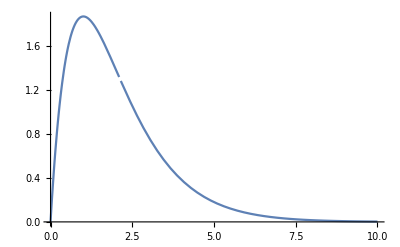

```mathematica
Plot[u,{d,0,10}]
```

```mathematica
Veff[0]
```

0